# PRACTICAL - 3

HARIOM (20201022)

Write parametric equations and make a parametric plot for an ellipse centered at the origin with horizontal major axis of 4 units and vertical minor axis of 2 units. Show the effect of rotation of this ellipse by an angle of ℼ/6 radians and shifting of the centre from (0,0) to (2,1) by making a parametric plot.

An ellipse centered at the origin with horizontal major axis of 4 units and vertical minor axis of 2 units is given by

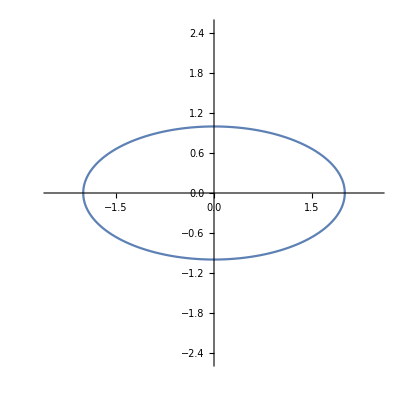

The effect of the rpotation of this ellipse by an angle of ℼ/6 radians and shifting of the centre from (0,0) to (2,1) is depicted in the following plot

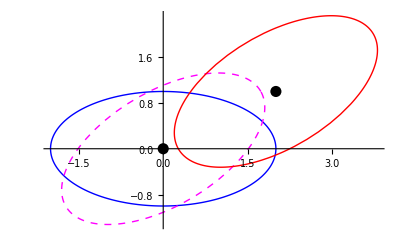

```mathematica
z[t_]:=2*Cos[t]+I*Sin[t];
Print["An ellipse centered at the origin with horizontal major axis of 4 units and vertical minor axis of 2 units is given by"];
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,2*Pi},PlotRange->2.5]
r[t_]:=z[t]*Exp[I*Pi/6];
s[t_]:=r[t]+(2+I);
Print["The effect of the rpotation of this ellipse by an angle of ℼ/6 radians and shifting of the centre from (0,0) to (2,1) is depicted in the following plot"];
Show[ParametricPlot[{{Re[z[t]],Im[z[t]]},{Re[r[t]],Im[r[t]]},{Re[s[t]],Im[s[t]]}},{t,0,2*Pi},PlotStyle->{{Blue,Thick},{Magenta,Dashed,Thick},{Red,Thick}}],Graphics[{PointSize[0.02],Point[{{0,0},{2,1}}]}]]
```